```mathematica
ClearAll["Global`*"]
```

# Separatrix plot - Phase diagram

```mathematica
f1[u_]:=1;
f2[u_]:=0;
f3[u_,v_]:=Sqrt[v];
f4[u_,v_]:=v;
f5[u_,v_]:=-v;
```

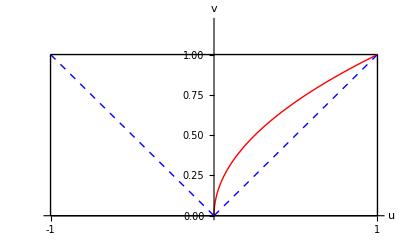

```mathematica
phaseD=Plot[{f1[u],f2[u],f3[u,u],f4[u,u],f5[u,u]},{u,-1,1},
PlotRange->{0,1.2},
AspectRatio->Automatic,
Frame->False,Axes->True,
Ticks->{{-1,1},None},
LabelStyle->{19,Black,FontFamily->"Latin Modern Roman"},
PlotStyle->{{Black,Thick},
{Black,Thick},
{Red,Thick},
{Blue,Thick,Dashed},
{Blue,Thick,Dashed}
},
AxesStyle->Directive[Thick,Black],
AxesLabel->{"u","v"}
];
Show[phaseD,Graphics[{Thick,Black,Line[{{1,0},{1,1}}]}],Graphics[{Thick,Black,Line[{{-1,0},{-1,1}}]}]]
```